# Unit 8 - Antiderivatives and Differential Equations

Topics covered in Unit 8 are listed below.

Antiderivatives and indefinite integrals

Solving differential equations of the form y'=f(x)

Solving differential equations of the form y'+P(x)y =Q(x)

Solving initial-value problems

Solving differential equations of the form y'=f(x,y)

Solving differential equations with DSolve and NDSolve

## Antiderivatives and indefinite integrals

Given a function f(x), if there is a function F(x) such that F'(x)=f(x), F(x) is called a antiderivative of f(x). The antiderivative of f(x) is not unique because, for any arbitrary constant C, (F(x)+C)'=F'(x)=f(x), i.e., F(x)+C is also an antiderivative of f(x). If G(x) is an antiderivative of f(x), there must be a constant C such that G(x)=F(x)+C.

The family of all antiderivatives of f(x) is called the indefinite integral of f(x) and denoted by ∫f(x)ⅆx. Thus,

∫f(x)ⅆx=F(x)+C.

We can use the palette, Palettes → Basic Math Assistant → Advanced, to type ∫f(x)ⅆx. We can also use EscintEsc and EscddEsc to type ∫ and ⅆ. Please be advised that ⅆ is not d or d. It is a special symbol. We can always use the full Mathematica name, Integrate, for ∫.

```mathematica
∫x^2 ⅆx
```

x^3/3

```mathematica
Integrate[x^2,x]
```

x^3/3

```mathematica
∫Sin[x]ⅆx
```

-Cos[x]

```mathematica
∫ⅇ^x ⅆx
```

ⅇ^x

```mathematica
∫ⅇ^x Sin[x]ⅆx
```

1/2 ⅇ^x (-Cos[x]+Sin[x])

```mathematica
∫Sin[x]^2 Cos[x]^5 ⅆx
```

(5 Sin[x])/64-1/192 Sin[3 x]-3/320 Sin[5 x]-1/448 Sin[7 x]

```mathematica
∫Sin[x]^2 Cos[x]^5 ⅆx//Simplify
```

1/840 (157+108 Cos[2 x]+15 Cos[4 x]) Sin[x]^3

We should notice that

(1) The Mathematica function does not include C, the constant of integration, in its output. When solving differential equations, we should not ignore the existence of such a constant term.
(2) By default, Mathematica does not simplify the algebraic expression returned from a function. Thus, we usually have to call Simplify when finding indefinite integral.

If F(x) is an antiderivative of f(x), i.e., F'(x)=f(x) or d/(d x)∫f(x)ⅆx=f(x).

```mathematica
D[∫Sin[x]^2 Cos[x]^5 ⅆx,x]
```

(5 Cos[x])/64-1/64 Cos[3 x]-3/64 Cos[5 x]-1/64 Cos[7 x]

which is not what we expected. Could Mathematica be wrong? No, we just need to apply Simplify to the result.

```mathematica
%//Simplify
```

Cos[x]^5 Sin[x]^2

```mathematica
{∫Sin[x^2] ⅆx,∫ⅇ^(x^2)ⅆx}
```

{√(π/2) FresnelS[√(2/π) x],1/2 √π Erfi[x]}

Whoops! We can't express the antiderivatives of sin x^2, e^(x^2), and some other functions, in terms of elementary functions. Mathematica can't either.

## Solving differential equations of the form y'=f(x)

An equation that contains an unknown function and its derivatives is called a differential equation. For example, (d y)/(d x)=2x+1 and (d^2 y)/(d x^2)+2x y (d y)/(d x)+y=5. It is usually tough to solve analytically a differential equation. But for simplest type of differential equations

(d y)/(d x)=f(x),

we can obtain the solution by finding the antiderivative of f(x) ,

y=∫f(x)ⅆx+C.

The solution to a differential equation involving arbitrary constant(s) is called a general solution to the equation. By assigning particular value(s) to the arbitrary constant(s), we obtain a particular solution. For example, y=x^2+C is the general solution to y'=2x, and y=x^2-1 is a particular solution.

Example 1
Solve the differential equation y'=2 sin x +3 x^2+5x-1.

```mathematica
Clear[x,f]
f[x_]:=2Sin[x]+3x^2+5x-1
∫f[x]ⅆx+C//TraditionalForm
```

C+x^3+(5 x^2)/2-x-2 cos(x)

Example 2
Find the general solution of y'=sin x and plot a family of solutions on one graph for -π≤x≤π.

C-1/2 Cos[2 x]

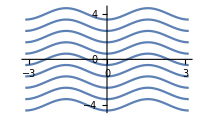

```mathematica
F[x_]=Integrate[Sin[2x],x]+C
Plot[Table[F[x],{C,-4,4}],{x,-Pi,Pi},ImageSize->200]
```

## Solving differential equations of the form y'+P(x)y=Q(x)

Another type of differential equations usually covered in a calculus class is the first-order linear differential equations. The equations can be rewritten in the standard form

(d y)/(d x)+P(x)y=Q(x) ⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯ (1)

To solve (1), we first find its integrating factor I(x),

ϕ(x)=ⅇ^(∫P(x)dx) ⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯ (2)

Then,

y=1/(ϕ(x))[∫ϕ(x)Q(x)d x+C] ⋯⋯⋯⋯⋯ (3)

where C is an arbitrary constant.

Example 3
Solve y'-2/x y=x^2 cos x,x>0.

```mathematica
μ[x_]:=ⅇ^Integrate[-2/x,x]
f[x_]=1/μ[x](Integrate[μ[x]*x^2 Cos[x],x]+C)
```

x^2 (C+Sin[x])

To verify if y=f(x) is truly a solution, we replace y by f(x) in the original differential equation, y'-2/x y=x^2 cos x, and verify if the equation is true.

```mathematica
f'[x]-2/x f[x]==x^2 Cos[x]
```

True

Example 4
Write a general function that solves any first-order differential equation in the standard form.

```mathematica
SolveFirstOrderLinearDiffEq[pfunc_,qfunc_] :=Module[{P,Q,μ},
P[X_]=pfunc/.x->X;
Q[X_]=qfunc/.x->X;
μ[x_]=E^Integrate[P[x],x];
1/μ[x] (Integrate[μ[x]Q[x],x]+C)]
```

```mathematica
SolveFirstOrderLinearDiffEq[-2/x,x^2 Cos[x]]
```

x^2 (C+Sin[x])

For y'+y=1+cos^2 x,

```mathematica
SolveFirstOrderLinearDiffEq[1,1+Cos[x]^2]
```

ⅇ^-x (C+1/10 ⅇ^x (15+Cos[2 x]+2 Sin[2 x]))

## Solving initial-value problems

In addition to differential equation(s), an initial-value problem provides also a number of initial conditions. After finding the general solution of the problem, we apply the initial conditions to determine particular values of the constants of integration in the general solution and obtain a particular solution.

Example 5
Solve the initial-value problem (d y)/(d x)=x^2 -2x+1,y(0)=1.

```mathematica
f[x_]:=x^2-2x+1
F[x_]=Integrate[f[x],x]+C
```

C+x-x^2+x^3/3

F(x) is a general solution to the differential equation. Now, we apply the initial condition y(0)=1 to determine the value of C in the general solution.

```mathematica
Solve[F[0]==1,C]//Flatten
```

{C→1}

Therefore, the particular solution will be

```mathematica
G[x_]=F[x]/.%
```

1+x-x^2+x^3/3

We can verify G(x)=1/3 x^3-x^2+x+1 is a particular solution of the very problem.

```mathematica
G'[x]==f[x] //Simplify (* is G(x) a solution to the differential equation? *)
```

True

```mathematica
G[0]==1 //Simplify (* is the initial condition met? *)
```

True

Example 6
Solve the initial-value problem, y'+y=1+cos^2 x,y(1)=2.

This is first-order linear differential equation in the standard form with P(x)=1 and Q(x)=1+cos^2 x. Thus, we can call the function SolveFirstOrderLinearDiffEq defined in previous section.

```mathematica
f[x_]=SolveFirstOrderLinearDiffEq[1,1+Cos[x]^2]//Simplify
```

1/10 (15+10 C ⅇ^-x+Cos[2 x]+2 Sin[2 x])

Now, apply the initial condition f(1)=2 to determine C in the general solution and, thus, obtain a particular solution.

```mathematica
cRule=Solve[f[1]==2,C]//Flatten
```

{C→-1/10 ⅇ (-5+Cos[2]+2 Sin[2])}

Thus, the particular solution is

```mathematica
F[x_]=f[x]/.cRule//Simplify
```

1/10 (15+Cos[2 x]-ⅇ^(1-x) (-5+Cos[2]+2 Sin[2])+2 Sin[2 x])

To verify y=F(x) is truly a particular solution, we first verify it satisfies the original differential equation,

```mathematica
F'[x]+F[x]==1+Cos[x]^2
```

1/10 (4 Cos[2 x]+ⅇ^(1-x) (-5+Cos[2]+2 Sin[2])-2 Sin[2 x])+1/10 (15+Cos[2 x]-ⅇ^(1-x) (-5+Cos[2]+2 Sin[2])+2 Sin[2 x])==1+Cos[x]^2

It is not a simple value of True as expected. We just have to apply Simplify to the result.

```mathematica
F'[x]+F[x]==1+Cos[x]^2//Simplify
```

True

This shows F(x) is a solution.

Now, we need to verify if F(x) satisfies the initial condition, y(1)=2,

```mathematica
F[1]
```

2

Therefore, F(x)=1/10 (15+cos(2x)-ⅇ^(1-x) (-5+cos 2+2 sin 2)+2 sin(2 x)) is a particular solution of the original differential equation.

Example 7
Solve the initial-value problems y''+2 y'=2x+1,y(0)=1,y'(0)=2.

This is a special second-order linear differential equation. Letting w=y', the initial-value problem can be converted to two initial-value problems, i.e.,

w'+2 w=2x+1,w(0)=2 ⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯ (4)
y'=w,y(0)=1  ⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯  (5)

We first solve (4), a first-order linear equation in the standard form, for w.

```mathematica
W[x_]=SolveFirstOrderLinearDiffEq[2,2x+1]
```

ⅇ^(-2 x) (C+ⅇ^(2 x) x)

Applying the initial condition w(0)=2, solve ⅇ^(-2 (0)) (C+ⅇ^(2(0)) (0))=2 for C.

```mathematica
Solve[W[0]==2,C]//Flatten
```

{C→2}

Therefore, a particular solution is

```mathematica
f[x_]=W[x]/.%//Simplify
```

2 ⅇ^(-2 x)+x

Now, solve (5), i.e., y'=2 ⅇ^(-2 x)+x,y(0)=1, for y.

```mathematica
F[x_]=Integrate[f[x],x]+C
```

C-ⅇ^(-2 x)+x^2/2

Apply the initial condition y(0)=1 to determine the constant of integration.

```mathematica
Solve[F[0]==1,C]//Flatten
```

{C→2}

Finally, the particular solution to the original initial-value problem is given by

```mathematica
H[x_]=F[x]/.%//Simplify
```

2-ⅇ^(-2 x)+x^2/2

If we need to verify if it is really the particular solution,

```mathematica
H''[x]+2H'[x]==2x+1//Simplify (* is it a solution to the original equation? *)
```

True

```mathematica
H[0]==1 (* is the first initial condition met? *)
```

True

```mathematica
H'[0]==2 (* is the second initial condition satisfied? *)
```

True

## Solving differential equations of the form y'=f(x,y)

Direction fields

Many differential equations of the form (d y)/(d x)=f(x,y) may not be easy to solve. But we know thatf(x,y) gives the slope of the tangent line to its solution curve at a point (x,y). In this sense, we say f(x,y) defines a direction (or slope) field in the x y-plane. Now, for a grid of points, if we draw a short line segment with slope f(x,y), with or without arrowhead, at each point (x,y), then, we can use these line segments to sketch the solution curve passing through a particular point (x_0,y_0), an initial condition. This approach is useful because, without finding an analytical solution to the differential equation, we can explore some important qualitative properties of the solution from the graphical representation.

Mathematica built-in function VectorPlot can be used to plot direction fields. Its basic usage is listed below.

VectorPlot[{f(x,y),g(x,y)},{x,x_min,x_max},{y,y_min,y_max}], generating a vector field {f(x,y),g(x,y)} as a function of x and y.

Vector and vector field

What is a vector? And what is a vector field? They are addressed in Calculus III. Simply speaking, a vector in the x y-plane is denoted by an ordered pair {a,b} (in 3-D space by {a,b,c} ). It has two aspects, its direction (graphically denoted by line segment with arrowhead) as well as its size or length. A vector field is a vector-valued function. For example, f(x,y)={ y,-x} is such a function. Confused? That is fine. Without the two concepts, we still can make VectorPlot work for our purpose.

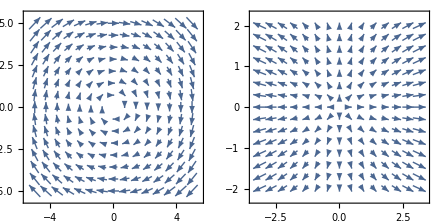

```mathematica
GraphicsRow[{
VectorPlot[{y,-x},{x,-5,5},{y,-5,5},ImageSize->200],
VectorPlot[{x,Sin[y]},{x,-Pi,Pi},{y,-2,2},ImageSize->200]
}]
```

Direction field of the first-order equation (d y)/(d x)=f(x,y)

At any point (x,y) on the x y-plane, the vector field of d/(d x){x,y}={(d x)/(d x),(d y)/(d x)}={1,f(x,y)} is called the direction field of the equation.

Example 8
Plot the slope field of the equation y'=x-y.

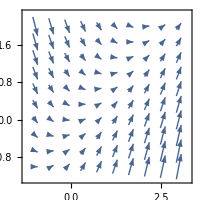

```mathematica
f[x_,y_]:=x-y
VectorPlot[{1,f[x,y]},{x,-1,3},{y,-1,2},VectorPoints->10,ImageSize->200]
```

Example 9
Plot the slope field of the equation y'=x-y together with six particular solutions.

```mathematica
DirectionFieldWithSolutionCurves[func_,{x_,xMin_,xMax_},{y_,yMin_,yMax_},numOfSoluCurves_:5]:=Module[{f,Y},
f[X_,Y_]=func/.{x->X,y->Y};
Y[c_]=y[x]/.DSolve[y'[x]==f[x,y[x]],y[x],x][[1]]/.C[1]->c;
Show[{
VectorPlot[{1,f[x,y]},{x,xMin,xMax},{y,yMin,yMax},VectorPoints->12,ImageSize->300],
Plot[Evaluate[Table[Y[c],{c,numOfSoluCurves}]],{x,xMin,xMax},PlotStyle->Map[Hue,0.85+.15Range[numOfSoluCurves]]]
}]
];
```

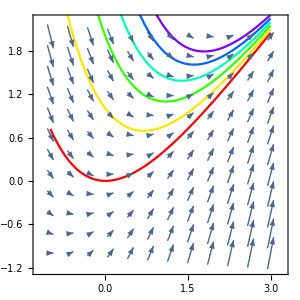

```mathematica
DirectionFieldWithSolutionCurves[x-y,{x,-1,3},{y,-1,2},6]
```

Example 10
Make an animation that, in the direction field of y'=f(x,y), find a particular solution passing through a specified point (x_0,y_0) as the point moves.

Description:
DirectionFieldPlot draws the slope field of y'=f(x,y), and sketches solution curves passing through points selected by mouse clicking. Clicking a previously selected point on the graph erases corresponding solution curve.

Usage:
                   func: the function f(x,y) as in y'=f(x,y)
{x,xMin,xMax}: the range of x appears on the graph
{y,yMin,yMax}: the range of y appears on the graph

```mathematica
(* v.1 on 7/4/15, v.2 on 7/6/15, by david wang dwang@liberty.edu *)
DirectionFieldPlot[func_,{x_,xMin_,xMax_},{y_,yMin_,yMax_}]:=
Manipulate[
DynamicModule[{f,Y,c,curves={},xy,new,i,count},
f[X_,Y_]=func/.{x->X,y->Y}; (* y' = f(x,y) *)
Y=y[x]/.DSolve[y'[x]==f[x,y[x]],y[x],x][[1]]/.C[1]->c;(* exact solution *)
EventHandler[
Dynamic[Show[{
VectorPlot[{1,f[x,y]},{x,xMin,xMax},{y,yMin,yMax},VectorPoints->16,VectorStyle->Arrowheads[0.018],ImageSize->300scale],
(* draw previous solution curves *)
count=Length[curves];
Plot[Table[Y/.c->curves[[i,2]],{i,count-1}],{x,xMin,xMax},PlotStyle->Blue],
Graphics[{Blue,PointSize[Large],Point[Table[curves[[i,1]],{i,count-1}]]}],
(* draw solution curve at newly selected point *)
If[count≥1,{
Graphics[{Red,PointSize[Large],Point[curves[[count,1]]]}],
Plot[Y/.c->curves[[count,2]],{x,xMin,xMax},PlotStyle->{Thick,Red}]
},{}] (* {} is required -:) *)
}]],
"MouseClicked":>(
xy=MousePosition["Graphics"];
(* to add a new curve or to remove a previous curve? *)
new=True; i=1;
While[i ≤ Length[curves], If[Total[ (curves[[i,1]]-xy)^2]<1/(10^2.3 scale),new=False;Break[]];i++];
curves=If[new,
Append[curves,{xy,c/.NSolve[(Y/.x->xy[[1]])==xy[[2]],c][[1]]}],
Delete[curves,i]]
)]
],{{scale,1,"Scale"},1,2.5,0.1}]
```

```mathematica
Clear[x,y]
DirectionFieldPlot[x-y,{x,-1,3},{y,-1,2}]
```

```mathematica
DirectionFieldPlot[6-2y,{x,0,3},{y,0,6}]
```

The method of isoclines for drawing direction field MANUALLY

A straightforward method to draw direction field manually is to construct a table consisting a number of chosen points (x,y) together with the slope at each point, then, at each point, draw a short line segment passing through the point with the corresponding slope. But this is time-consuming.

For any given constant c, y'=f(x,y)=c means that, at each point on the curve of f(x,y)=c, the slope is always y'=c. Therefore, we draw the curve f(x,y)=c first and then draw a line segment with slope y'=c at each chosen point on the curve. These line segments are called isoclines. We repeat this process for each of a number of chosen c values. Finally, we erase all curves f(x,y)=c and obtain the slope field of the differential equation y'=f(x,y). If f(x,y)=c is some basic curve, such as a straight line, a parabola, a circle, or an ellipse, this method of isoclines can help us quickly draw the direction field of y'=f(x,y).

Example 11
Use the method of isoclines to draw the direction field of y'=x^2-y near the point of (0,0).

The following function draws count isoclines of y'=f(x,y)=c on the region [xmin,xmax]×[ymin,ymax]. Each line segment has the length len.

```mathematica
DrawIsoclines[func_,xmin_,xmax_,ymin_,ymax_,c_,count_,len_]:=Module[{h,eqn,isoclineY, lineSeg},
eqn[X_,Y_]:=func/.{x->X,y->Y};
isoclineY[x_,x0_,y0_]:=y0+c(x-x0);
h=(xmax-xmin)/count;
lineSeg[x_,y_]:=Module[{x1,x2},
{x1,x2}=x1/.NSolve[(x1-x)^2+(isoclineY[x1,x,y]-y)^2==len^2,x1];
Line[{{x1,isoclineY[x1,x,y]},{x2,isoclineY[x2,x,y]}}]
];
Show[{
ContourPlot[eqn[x,y]==c,{x,xmin,xmax},{y,ymin,ymax},ContourStyle->LightGray,ImageSize->250],
Graphics[{Thin,Black,Table[Module[{ys},
ys=y/.NSolve[eqn[x,y]==c,y];
Table[lineSeg[x,y],{y,ys}]],{x,xmin,xmax,h}]}]
}]
];
```

For example, the isoclines corresponding to c=1 look like

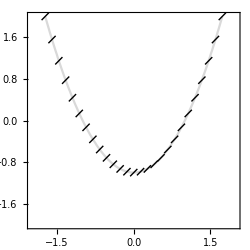

```mathematica
DrawIsoclines[x^2-y,-2,2,-2,2,1,30,.1]
```

Now, we plot isoclines corresponding to a number of c values.

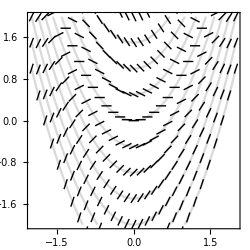

```mathematica
Show[Table[DrawIsoclines[x^2-y,-2,2,-2,2,c,30,.1],{c,-3,3,0.5}]]
```

The next animation displays the process of drawing isoclines.

```mathematica
Manipulate[Module[{DrawIsoclines},
DrawIsoclines[func_,xmin_,xmax_,ymin_,ymax_,c_,count_,len_]:=Module[{h,eqn,isoclineY, lineSeg},
eqn[X_,Y_]:=func/.{x->X,y->Y};
isoclineY[x_,x0_,y0_]:=y0+c(x-x0);
h=(xmax-xmin)/count;
lineSeg[x_,y_]:=Module[{x1,x2},
{x1,x2}=x1/.NSolve[(x1-x)^2+(isoclineY[x1,x,y]-y)^2==len^2,x1];
Line[{{x1,isoclineY[x1,x,y]},{x2,isoclineY[x2,x,y]}}]
];
Show[{
ContourPlot[eqn[x,y]==c,{x,xmin,xmax},{y,ymin,ymax},ContourStyle->LightGray,ImageSize->250],
Graphics[{Thin,Black,Table[Module[{ys},
ys=y/.NSolve[eqn[x,y]==c,y];
Table[lineSeg[x,y],{y,ys}]],{x,xmin,xmax,h}]}]
}]
];
DrawIsoclines[x^2-y,-2,2,-2,2,c,30,.1]
],{{c,0},-2,3,0.5,Appearance->"Open"}]
```

Euler’s method

Even algebraic equations are usually difficult to solve. For example, can you solve manually the equations, x^5-9 x^2+4x-1=0, 4x+sin x=1, 4x ⅇ^x-3 x=20, ln x+2 x^2-1=0, to randomly name a few. When differential equations are concerned, things are getting much more complicated and difficult. Honestly speaking, we can only solve some types of simplified equations. But the Creator has given us intelligence to invent computer, and ability to invent algorithms and program computer and have it work for us. We have intelligence, and computer has patience and speed. The combination of human intelligence and computer’s power leads to the solution of much more equations.

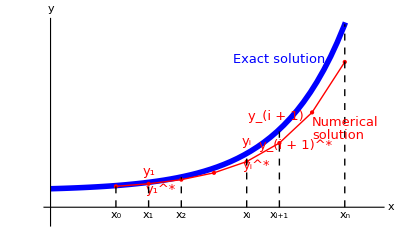
-Graphics-Euler's method for y'=f(x,y),y(x_0)=y_0

Euler’s method for solving the initial-value problem, y'=f(x,y),y(x_0)=y_0, is a basic approach. The basic idea is to use connected line segments to approximate the exact solution of the problem. Then, how should we choose or determine the line segments? Start from the given initial point (x_0,y_0), we know the slope of the tangent line at the point is given by y'=f(x_0,y_0) from which the equation of the tangent line is

y=y_0+f(x_0,y_0)(x-x_0).

If we move to x_1from x_0, the equation gives y_1^*=y_0+f(x_0,y_0)(x_1-x_0), which is a good approximation to the exact value y_1 if x_1 is close enough to x_0, as shown in the figure. Now, assume (x_1,y_1^*) is on the solution curve. Start from the point, find the equation of the line tangent to the solution curve, and compute (x_2,y_2^*) which is possibly still a good approximation to the point (x_2,y_2) on the solution curve. Now, assume we are at the point (x_i,y_i^*). We are to find the iterative formula for computing the next point (x_(i+1),y_(i+1)^*). The tangent line at (x_i,y_i^*) is given by

y=y_i^*+f(x_i,y_i^*)(x-x_i).

So,

y_(i+1)^*=y_i^*+f(x_i,y_i^*)(x_(i+1)-x_i).

Therefore, if the domain [a,b] is evenly divided into n subintervals with x_0=a, x_n=b, x_(i+1)-x_i=h=(b-a)/n, the iterative formula for Euler’s method is

{x_(i+1)=x_i+h
y_(i+1)^*=y_i^*+f(x_i,y_i^*)h for i=0,1,2,⋯,n.

Due to accumulated truncation and rounding errors, the approximation is getting worse and worse when we calculate at points away from (x_0,y_0). Using more data points (i.e., larger value of n) can reduce truncation error and produce better approximation. The following animation may help you understand all these. By the way, numerically, we cannot increase the value of n without constraint. A larger value of n demands more computing time and memory as well. Moreover, the accumulated rounding error might be a problem itself.

Example 12
Write a function that animates Euler’s method for y'=f(x,y),y(x_0)=y_0 with n changeable.

Usage:
            func: the function f(x,y) as in y'=f(x,y)
           Func: the exact solution to y'=f(x,y)
        {x_0.y_0}: the initial condition y(x_0)=y_0
          {a,b}: the domain over which numerical solution is sought; also the plot range of x
 plotOptions: some Plot options, such as PlotRange→{-1,2}

```mathematica
AnimateEulerMethod[func_,Func_,{x0_,y0_},{a_,b_},plotOptions___]:=
Manipulate[
Module[{f,F,h,points},
f[X_,Y_]=func/.{x->X,y->Y};
F[X_]=Func/.{x->X,y->Y};

h=(b-a)/n;
euler[{x_,y_}]:={x+h,y+f[x,y]*h};
points=NestList[euler,{x0,y0},n];

Show[{
Plot[F[x],{x,a,b},PlotStyle->{Blue,Thickness[0.01]},plotOptions,ImageSize->330],
ListPlot[points,PlotStyle->{Red,PointSize[Medium]}],
Graphics[{Red,Line[points]}]
}]
],{{n,20},1,200,1,Appearance->"Open"}]
```

```mathematica
Clear[x]
AnimateEulerMethod[1/15 ⅇ^x,1/15 ⅇ^x+14/15,{0,1},{0,5},PlotRange->{0,10}]
```

Example 13
Use Euler’s method to find and plot the approximate solution to y'=x-y^2+2, y(0)=2 for 0≤x≤2 with n=30.

```mathematica
f[x_,y_]:=x-y^2+2;
a=0;b=2.;n=30;
h=(b-a)/n;

euler[{x_,y_}]:={x+h,y+f[x,y]*h};
points=NestList[euler,{0,2},n] (* initial condition y(0)=2 *)
```

{{0,2},{0.0666667,1.86667},{0.133333,1.77215},{0.2,1.705},{0.266667,1.65787},{0.333333,1.62574},{0.4,1.6051},{0.466667,1.59334},{0.533333,1.58854},{0.6,1.5892},{0.666667,1.59416},{0.733333,1.60251},{0.8,1.61353},{0.866667,1.62663},{0.933333,1.64135},{1.,1.6573},{1.06667,1.67419},{1.13333,1.69178},{1.2,1.70986},{1.26667,1.72828},{1.33333,1.74693},{1.4,1.7657},{1.46667,1.78452},{1.53333,1.80333},{1.6,1.82209},{1.66667,1.84075},{1.73333,1.85931},{1.8,1.87773},{1.86667,1.896},{1.93333,1.91413},{2.,1.93209}}

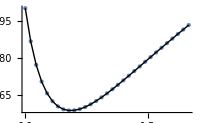

```mathematica
Show[{
ListPlot[points,PlotStyle->PointSize[Medium],ImageSize->200],
Graphics[Line[points]]
}]
```

## Solving differential equations with DSolve and NDSolve

Quite similar to Solve and NSolve, DSolve and NDSolve can be used to solve a differential equation or a system of differential equations.  DSolve finds exact solution, while NDSolve gives numerical approximation of the exact solution.

The usage of DSolve and NDSolve is similar. But for NDSolve， the numerical approximation requires the domain of functions to be found, i.e., the intervals of each independent variable.

DSolve[eqn(s),y,x], solving the ordinary differential equation eqn(s) for y(x).

DSolve[{eqn_1,eqn_2,…},{y_1,y_2,…},x], solving a system of differential equations for y_1(x),y_2(x),⋯.

NDSolve[eqns,y,{x,x_min,x_max}], solving numerically the initial-value problem eqns for y(x).

NDSolve[eqns,{y_1,y_2,…},{x,x_min,x_max}], solving numerically a system of differential equations for y_1(x),y_2(x),⋯.

Listed below are the other two usages pertaining to multivariable functions covered in Calculus III and advanced mathematics courses.

DSolve[eqn(s),y,{x_1,x_2,…}], solving the partial differential equation eqn(s) for y(x_1,x_2,⋯).

NDSolve[eqns,y,{x,x_min,x_max},{t,t_min,t_max}], solving numerically the partial differential equation eqns for y(x,t).

DSolve for one differential equation

Both DSolve and NDSolve require us to specify explicitly that y is a function of x or x_1,x_2,⋯ by the notation y[x] or y[x_1,x_2,⋯]. This is not new to us for implicit differentiation in Unit 6 has the same requirement.

Example 14
Find a general solution to the differential equation y' = x^2 sin x.

```mathematica
y[x]/.DSolve[y'[x]==x^2 Sin[x],y[x],x]
```

{C[1]-(-2+x^2) Cos[x]+2 x Sin[x]}

where C[1] denotes an arbitrary constant.

Example 15
Find the particular solution to the initial-value problem y' = x^2 sin x,y(0)=2.

We may solve it in two steps. First, find a general solution to y'=x^2 sin x..

```mathematica
f[x_]=(y[x]/.DSolve[y'[x]==x^2 Sin[x],y[x],x])[[1]]
```

C[1]-(-2+x^2) Cos[x]+2 x Sin[x]

Second, find the particular solution, applying the initial condition y(0)=2.

```mathematica
Solve[f[0]==2,C[1]]
```

{{C[1]→0}}

```mathematica
f[x_]=f[x]/.%[[1]]
```

-(-2+x^2) Cos[x]+2 x Sin[x]

```mathematica
%//TraditionalForm
```

2 x sin(x)-(x^2-2) cos(x)

which is the particular solution.

DSolve allows us to solve directly an initial-value problem.

```mathematica
DSolve[{y'[x]==x^2 Sin[x],y[0]==2},y[x],x]//Simplify
```

{{y[x]→-(-2+x^2) Cos[x]+2 x Sin[x]}}

DSolve for a system of differential equations

Example 16
Solve the system x'=3x-5y+2,y'=2x+y-6t, where x and y are each a function of t.

```mathematica
Clear[x,y,t]
DSolve[{x'[t]==3x[t]-5y[t]+2,y'[t]==2x[t]+y[t]-6t},{x[t],y[t]},t]//Simplify
```

{{x[t]→2/169 (47+195 t)+ⅇ^(2 t) C[1] Cos[3 t]+1/3 ⅇ^(2 t) (C[1]-5 C[2]) Sin[3 t],y[t]→2/169 (23+117 t)+ⅇ^(2 t) C[2] Cos[3 t]+1/3 ⅇ^(2 t) (2 C[1]-C[2]) Sin[3 t]}}

where C[1] and C[2] are two arbitrary constants.

Example 17
Solve the system x'=3x-5y+2,y'=2x+y-6t, where x and y are each a function of t, with the initial condition x(0)=1,y(0)=3.

```mathematica
Clear[x,y,t]
DSolve[{
(* differential equations *)
x'[t]==3x[t]-5y[t]+2,
y'[t]==2x[t]+y[t]-6t,

(* initial conditions *)
x[0]==1,y[0]==3 
},{x[t],y[t]},t]//Simplify
```

{{x[t]→1/507 (282+1170 t+225 ⅇ^(2 t) Cos[3 t]-2230 ⅇ^(2 t) Sin[3 t]),y[t]→1/507 (138+702 t+1383 ⅇ^(2 t) Cos[3 t]-311 ⅇ^(2 t) Sin[3 t])}}

```mathematica
{x[t_],y[t_]}={x[t],y[t]}/.%[[1]]
```

{1/507 (282+1170 t+225 ⅇ^(2 t) Cos[3 t]-2230 ⅇ^(2 t) Sin[3 t]),1/507 (138+702 t+1383 ⅇ^(2 t) Cos[3 t]-311 ⅇ^(2 t) Sin[3 t])}

We can verify if they are truly the solution.

```mathematica
{x'[t]==3x[t]-5y[t]+2,y'[t]==2x[t]+y[t]-6t,x[0]==1,y[0]==3}//Simplify
```

{True,True,True,True}

NDSolve for one differential equation

Example 18
Use NDSolve to solve the initial-value problem x^2 y''-(y')^2+2x sin y+1=0, y(1)=1,y'(1)=0 for 0<x≤8.

```mathematica
Clear[x,y]
NDSolve[{x^2*y''[x]-(y'[x])^2+2x*Sin[y[x]]+1==0,y[1]==1,y'[1]==0},y,{x,10^-16,8}]
```

{{y→                             -16
InterpolatingFunction[{{1. 10   , 8.}}, <>]}}

It returns a function that evaluates the Mathematica built-in InterpolatingFunction. Refer to introduction at the end of this section for interpolation technique.

```mathematica
f=y/.%[[1]]
```

-16
InterpolatingFunction[{{1. 10   , 8.}}, <>]

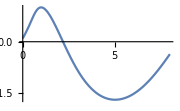

```mathematica
Plot[f[x],{x,0,8},PlotRange->All,ImageSize->180]
```

NDSolve for a system of differential equations

Example 19
Solve the system x'=-sin(3x)-y,y'=x-cos y, where x and y are each a function of t for 0≤t≤50, with the initial condition x(0)=1,y(0)=0.

```mathematica
Clear[x,y]
{f,g}={x,y}/.NDSolve[{x'[t]==-Sin[3x[t]]-y[t],y'[t]==x[t]-Cos[y[t]],x[0]==1,y[0]==0},{x,y},{t,50}][[1]]
```

{InterpolatingFunction[{{0., 50.}}, <>],InterpolatingFunction[{{0., 50.}}, <>]}

These functions x=f[t] and y=g[t] are the parametric equations for some curve. So, we can plot the curve using ParametricPlot (See Unit 10).

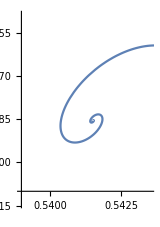

```mathematica
ParametricPlot[{f[t],g[t]},{t,0,50},ImageSize->160]
```

Interpolation - Interpolation and InterpolatingFunction

The Mathematica built-in function InterpolatingFunction works like Function. It gives an approximate function whose values are computed by interpolation, a technique by which a mathematical formula is derived to represent a set of given data points such that it gives the exact value at every given data point and an estimated value at any other point in the range of the data set. Numerical computing class like MATH 352 shall address the technique in detail.

```mathematica
points = {{0,0},{1,0.5},{2,1.5},{3,2.6},{4,2.5},{5,0.5},{7,0}};
f=Interpolation[points]
```

InterpolatingFunction[{{0., 7.}}, <>]

```mathematica
f[5] (* y value at a given point *)
```

0.5

```mathematica
f[1.53] (* y value at a point which is not in the data set but in the range of data *)
```

0.993133

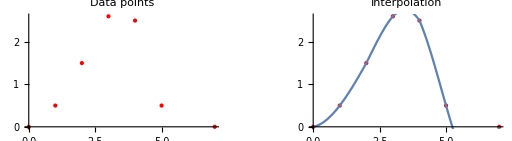

```mathematica
GraphicsRow[{
ListPlot[points,ImageSize->200,PlotStyle->{Red,PointSize[Medium]},PlotLabel->"Data points"],
Show[{
ListPlot[points,ImageSize->200,PlotStyle->{Red,PointSize[Medium]},PlotLabel->"Interpolation"],
Plot[f[x],{x,0,7}]
}]
},Spacings->50]
```

## Lab 8

Find the antiderivative of each function with the help of Mathematica, then, verify the result by finding its derivative. Remember that you might have to apply Simplify.

f(x)=x^3-3x+3

f(x)=(x-1)/(x(x+1))

f(x)=ⅇ^x cos x

f(x)=x^2 sin 3x

Without using DSolve or NDSolve, solve each initial-value problem and plot its solution.

y'=2x cos x,y(0)=2

y''=2x -1,y(1)=0,y'(1)=2

y'+2/x y=x+1,y(1)=1,x>0

Using DSolve, solve the initial-value problem y'=2x cos x,y(0)=2.

Using DSolve, solve the initial-value problem y''=2x -1,y(1)=0,y'(1)=2.

Using DSolve, find a general solution to the differential equation y'=y^2 cos x-2y.

Using NDSolve, solve y'=y^2 cos x-2y,y(0)=1, for 0<x≤2π, and plot your numerical solution.

Given the following data set, use Interpolation to find an interpolation of the data set, plot the interpolating function, and estimate the value of y at x=1.5 and 4.34, respectively.

```mathematica
{{1,5},{2,5},{3,1},{4,1},{5,3},{6,4},{7,6},{8,5},{9,0},{10,2}}
```

Plot the slope field of the equation y'=sin x cos y together with five particular solutions for -3≤x≤3 and -3≤y≤3.

Use the function DirectionFieldPlot to play with y'=sin x for -2π≤x≤2π and -3≤y≤3. What analytical solution does the slope field suggest in general? Tips: You had better copy and paste the code for DirectionFieldPlot to your solution here first.

Using the function AnimateEulerMethod, play with y'=sin x, y(0)=1 on the interval [0,2π]. Tips: The exact solution is y=2-cos x. You had better copy and paste the code for  AnimateEulerMethod to your solution here first.

Use Euler’s method to find and plot the approximate solution to y'=1+x sin x, y(1)=2 for 1≤x≤2π with n=20.

© 2015-2023 by David Wang, dwang@liberty.edu